#### Kuehn’s formulas

```mathematica
Σ=√0.8;
Subscript[Γ, 3][y_]:=Gamma[1+2 y/Σ^2];
Subscript[Γ, 4][y_]:=Gamma[2 y/Σ^2];
v1[y_]:=y^2;
v2[y_]:=1/2 y Σ^2;
v3[y_]:=-4^(-y/Σ^2)y(1/Σ^2)^(-2 y/Σ^2)Σ^2 Subscript[Γ, 3][y];
v4[y_]:=2^(-4 y/Σ^2)y^2(1/Σ^2)^(-4 y/Σ^2)(Subscript[Γ, 4][y])^2;
v[y_]:=v1[y]+v2[y]+v3[y]+v4[y];
m[y_]:=4^(-y/Σ^2)y(1/Σ^2)^(-2 y/Σ^2)Subscript[Γ, 4][y];
yvalues = Range[0.1,3,0.01];
theoreticalMean = ConstantArray[0,Length[yvalues]-1];
theoreticalVariance = ConstantArray[0,Length[yvalues]-1];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,1000];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
theoreticalMean[[j]]=N[m[Y]];
theoreticalVariance[[j]]=N[v[Y]];
];
Print[theoreticalMean]
Print[theoreticalVariance]
```

#### A&B definitions

```mathematica
Σ=√0.8;
Subscript[n, 1][y_]:=Gamma[2 y/Σ^2](Σ^2/2)^(2 y/Σ^2);
Subscript[n, 2][y_]:=∫_0.01^(+∞) x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2)ⅆx;
p[x_,y_]:=(Subscript[n, 2][y])^-1 x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
μ[y_]:=∫_0.01^(+∞) x p[x,y]ⅆx;
var[y_]:=∫_0.01^(+∞) (x-μ[y])^2 p[x,y]ⅆx;
yvalues = Range[0.1,3,0.01];
FPMean = ConstantArray[0,Length[yvalues]-1];
FPVariance = ConstantArray[0,Length[yvalues]-1];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,1000];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
(*FPMean[[j]]=N[μ[Y]];*)
FPMean[[j]]=NIntegrate[x p[x,Y],{x,0,+∞},Method->{"LocalAdaptive"}];
(*FPVariance[[j]]=N[var[Y]];*)
FPVariance[[j]]=NIntegrate[(x-FPMean[[j]])^2 p[x,Y],{x,0,+∞},Method->{"LocalAdaptive"}];;
];
Print[FPMean]
Print[FPVariance]
```

#### F-P distribution @ fixed y-values

```mathematica
Subscript[n, 2][y_]:=(∫_0.01^(+∞) x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2)ⅆx)^-1;
p[x_,y_]:=Subscript[n, 2][y] x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
yvaluesNew = List[0.39292,0.68585,0.97878,1.27127,1.56464,1.85757,2.15050,2.44343];
xvalues = Range[0.01,6,0.1];
distro = ConstantArray[0,Length[xvalues]-1];
For[j=1,j< Length[yvaluesNew],j++,
Y=yvaluesNew[[j]];
distro = ConstantArray[0,Length[xvalues]-1];
For[k=1,k< Length[xvalues],k++,
X=xvalues[[k]];
distro[[k]]=N[p[X,Y]];
];
Print[distro]
];
```

#### Normalization constant

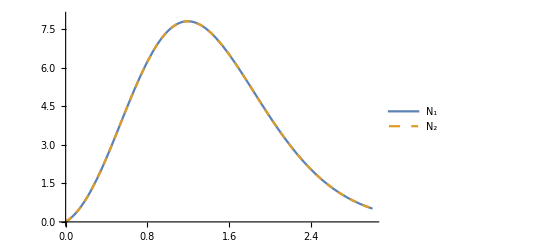

```mathematica
Σ=√0.8;
Subscript[n, 1][y_]:=Gamma[2 y/Σ^2](Σ^2/2)^(2 y/Σ^2);
f[x_,y_]:=x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
Subscript[n, 2][y_]:=NIntegrate[f[x,y],{x,0,+∞},Method->{"LocalAdaptive","SingularityHandler"-> "DoubleExponential"},PrecisionGoal->10, Exclusions->{0}];
Plot[{(Subscript[n, 1][y])^-1,(Subscript[n, 2][y])^-1},{y,0,3},PlotRange->{0, 8},PlotLegends->{"N_1","N_2"}, PlotStyle->{Thick,Dashed}]
```

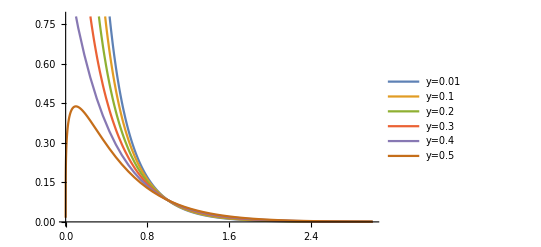

```mathematica
(*https://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html*)
Y=0.1;
f[x_,y_]:=x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
g[x_]:=f[x,Y];
Plot[{f[x,0.01],f[x,0.1],f[x,0.2],f[x,0.3], f[x,0.4], f[x,0.5]},{x,0,3},PlotLegends->{"y=0.01", "y=0.1", "y=0.2", "y=0.3", "y=0.4", "y=0.5"}]
```